```mathematica
(*Mathematica
(*Gell-Mann SU(3)*)*)
```

```mathematica
s[1]={{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
s[2]={{0,-I,0},{I,0,0},{0,0,0}};
```

```mathematica
s[3]={{1,0,0},{0,-1,0},{0,0,0}};
```

```mathematica
s[4]={{0,0,1},{0,0,0},{1,0,0}};
```

```mathematica
s[5]={{0,0,-I},{0,0,0},{I,0,0}};
```

```mathematica
s[6]={{0,0,0},{0,0,1},{0,1,0}};
```

```mathematica
s[7]={{0,0,0},{0,0,-I},{0,I,0}};
```

```mathematica
s[8]={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
```

```mathematica
s[9]={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Cycle:Octagon*)
```

```mathematica
Apply[Dot,Table[s[i],{i,8}]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[Det[s[i]],{i,8}]
Table[Tr[s[i]],{i,8}]
```

{0,0,0,0,0,0,0,-2/(3 √3)}

{0,0,0,0,0,0,0,0}

```mathematica
(*Casimir invariant*)
ci=Sum[s[i].s[i],{i,8}]
```

{{16/3,0,0},{0,16/3,0},{0,0,16/3}}

```mathematica
(*Complex Pseudo-Salem Polynomial*)
```

```mathematica
p[x_]=(1-x^3-x^4-x^5+x^8)
```

1-x^3-x^4-x^5+x^8

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
w=Table[r[i],{i,8}]
```

{-0.882007-0.471235 ⅈ,-0.882007+0.471235 ⅈ,-0.346911-0.937898 ⅈ,-0.346911+0.937898 ⅈ,0.198169-0.980168 ⅈ,0.198169+0.980168 ⅈ,0.780861,1.28064}

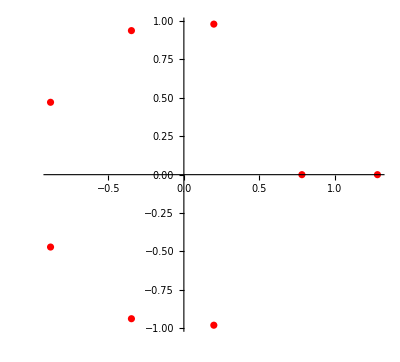

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
(*SL(3,c) matrix*)
```

```mathematica
(*/(0.45669694918424186+7.471506281091266 ⅈ)^(1/3)*)
```

```mathematica
m=(s[9]+Sum[s[i]*r[i],{i,8}])/(0.37355805346686144+8.11985875924096 ⅈ)^(1/3)
```

{{0.377983-0.744539 ⅈ,-0.0790461+0.277898 ⅈ,-0.39754+0.642612 ⅈ},{-0.915505-0.260409 ⅈ,1.13347-0.0974814 ⅈ,0.134342+0.0386287 ⅈ},{0.550119+0.340321 ⅈ,0.512352+0.717165 ⅈ,-0.208009+0.115881 ⅈ}}

```mathematica
dt=Det[m]//Chop
```

1.

```mathematica
Tr[m]
```

1.30344-0.72614 ⅈ

```mathematica
msl=(s[9]+Sum[s[i]*(z-r[i]),{i,8}])/(0.37355805346686144+8.11985875924096 ⅈ)^(1/3)
```

{{(0.43448-0.242047 ⅈ) ((1.34691+0.937898 ⅈ)+(-1.28064+z)/(√3)+z),(0.43448-0.242047 ⅈ) ((0.882007+0.471235 ⅈ)+z-ⅈ ((0.882007-0.471235 ⅈ)+z)),(0.43448-0.242047 ⅈ) ((0.346911-0.937898 ⅈ)-ⅈ ((-0.198169+0.980168 ⅈ)+z)+z)},{(0.43448-0.242047 ⅈ) ((0.882007+0.471235 ⅈ)+z+ⅈ ((0.882007-0.471235 ⅈ)+z)),(0.43448-0.242047 ⅈ) ((0.653089-0.937898 ⅈ)+(-1.28064+z)/(√3)-z),(0.43448-0.242047 ⅈ) ((-0.198169-0.980168 ⅈ)-ⅈ (-0.780861+z)+z)},{(0.43448-0.242047 ⅈ) ((0.346911-0.937898 ⅈ)+ⅈ ((-0.198169+0.980168 ⅈ)+z)+z),(0.43448-0.242047 ⅈ) ((-0.198169-0.980168 ⅈ)+ⅈ (-0.780861+z)+z),(0.43448-0.242047 ⅈ) (1-(2 (-1.28064+z))/(√3))}}

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/((0.0684564414791865-2.268813962494383 ⅈ))]//Chop
```

(0.0950988-0.438644 ⅈ)-(0.769481+0.483428 ⅈ) z+(0.441045+0.955112 ⅈ) z^2+1. z^3

```mathematica
v=z/.NSolve[f[z]==0,z]
```

{-0.916002-0.729494 ⅈ,-0.298081-0.383588 ⅈ,0.773038+0.15797 ⅈ}

```mathematica
max=Max[Norm/@v]+0.75
```

1.92099

```mathematica
(1.075+1.1)/2
```

1.0875

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
g1=JuliaSetPlot[f[x]*1.0875,x,ColorFunction->"Rainbow",ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x]*1.0875,x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1];
Export["Julia_SU3_Pseudo-Salem_Polynomial_scale_1p0875_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->{4000,4000}]]
```

Julia_SU3_Pseudo-Salem_Polynomial_scale_1p0875_grid.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]*1.0875;
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-max+0.0001,max,1000},{-max-0.5,max-0.5,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g1.jpg",g1]
```

j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g1.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g2.jpg",g2]
```

j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g3.jpg",g3]
```

j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_g3.jpg

```mathematica
Export["j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

j_1000_SU3_Pseudo-Salem_Polynomial_In_Out_monitor_grid.jpg

```mathematica
(*end*)
```